```mathematica
ClearAll["Global`*"]
(* Here we will solve Equation 26 using the KBM method *)

(* These are the Ansatz that we will choose, and now we will solve Eq. 26 for both A[T] and Φ[T] *)
x0[T_]:=A[T]*Sin[T+Φ[T]];
x1[T_]:=A[T]*Cos[T+Φ[T]];

(* Source term of Equation 31; We use "KK[T]" and not "K[T]" because "K" is protected in Wolfram Mathematica *)
KK[T_]:=μ*(1-x0[T])*(1+σ*x0[T])*x1[T]-ϵ*α*Sin[ω*T]*x0[T]-β*(1+ϵ*Sin[ω*T])*x0[T]^2-γ*(1+ϵ*Sin[ω*T])*x0[T]^3+F*(0+ϵ*Sin[ω*T]);

(* Set of equations do be solved *)
eq1=x1'[T]+x0[T]== KK[T];
eq2=x1[T]== x0'[T];

(* Isolating A'[T] and Φ'[T] *)
exactEDO=Solve[{eq1,eq2},{A'[T],Φ'[T]}][[1]]//Simplify
```

{A'[T]→-Cos[T+Φ[T]] (-F ϵ Sin[T ω]+A[T] (-μ Cos[T+Φ[T]]+α ϵ Sin[T ω] Sin[T+Φ[T]])+A[T]^3 Sin[T+Φ[T]]^2 (μ σ Cos[T+Φ[T]]+γ (1+ϵ Sin[T ω]) Sin[T+Φ[T]])+1/2 A[T]^2 (2 β (1+ϵ Sin[T ω]) Sin[T+Φ[T]]^2-μ (-1+σ) Sin[2 (T+Φ[T])])),Φ'[T]→1/A[T]Sin[T+Φ[T]] (-F ϵ Sin[T ω]+A[T] (-μ Cos[T+Φ[T]]+α ϵ Sin[T ω] Sin[T+Φ[T]])+A[T]^3 Sin[T+Φ[T]]^2 (μ σ Cos[T+Φ[T]]+γ (1+ϵ Sin[T ω]) Sin[T+Φ[T]])+1/2 A[T]^2 (2 β (1+ϵ Sin[T ω]) Sin[T+Φ[T]]^2-μ (-1+σ) Sin[2 (T+Φ[T])]))}

```mathematica
(* Removing the nonautonomous term, i.e., the 'T' variable *)
preKBMeq=exactEDO/.{A[T]->A,Φ[T]->Φ,T->ψ-Φ}
```

{A'[-Φ+ψ]→-Cos[ψ] (-F ϵ Sin[(-Φ+ψ) ω]+A (-μ Cos[ψ]+α ϵ Sin[ψ] Sin[(-Φ+ψ) ω])+A^3 Sin[ψ]^2 (μ σ Cos[ψ]+γ Sin[ψ] (1+ϵ Sin[(-Φ+ψ) ω]))+1/2 A^2 (-μ (-1+σ) Sin[2 ψ]+2 β Sin[ψ]^2 (1+ϵ Sin[(-Φ+ψ) ω]))),Φ'[-Φ+ψ]→1/A Sin[ψ] (-F ϵ Sin[(-Φ+ψ) ω]+A (-μ Cos[ψ]+α ϵ Sin[ψ] Sin[(-Φ+ψ) ω])+A^3 Sin[ψ]^2 (μ σ Cos[ψ]+γ Sin[ψ] (1+ϵ Sin[(-Φ+ψ) ω]))+1/2 A^2 (-μ (-1+σ) Sin[2 ψ]+2 β Sin[ψ]^2 (1+ϵ Sin[(-Φ+ψ) ω])))}

```mathematica
(* Here we are construction the KBM equations for both amplitude A[T] and the phase correction Φ[T], which is accomplished by taking the average over one period of the system, i.e., θ ∈ [0, 2π], letting both 'A' and 'Φ' constant during this integration, and that is the KBM approximation *)

(* These are Equations 39 and 40 from the Supplementary Material *)
KBMA=(Integrate[preKBMeq[[1]][[2]],{ψ,0,2π}]/(2π))/.{A-> A[T], Φ-> Φ[T]}//Simplify;
KBMA=(A'[T]==KBMA)
KBMΦ=(Integrate[preKBMeq[[2]][[2]],{ψ,0,2π}]/(2π))/.{A-> A[T], Φ-> Φ[T]}//Simplify;
KBMΦ=(Φ'[T]==KBMΦ)
```

A'[T]==((F ϵ ω (Cos[ω Φ[T]]-Cos[ω (-2 π+Φ[T])]))/(-1+ω^2)+A[T] (π μ-(2 α ϵ Cos[ω (π-Φ[T])] Sin[π ω])/(-4+ω^2))+A[T]^3 (-1/4 π μ σ+(12 γ ϵ Cos[ω (π-Φ[T])] Sin[π ω])/(64-20 ω^2+ω^4))+(4 β ϵ ω A[T]^2 Sin[π ω] Sin[ω (π-Φ[T])])/(9-10 ω^2+ω^4))/(2 π)

Φ'[T]==3/8 γ A[T]^2-(ϵ (F (-9+ω^2)+6 β A[T]^2) Cos[ω (π-Φ[T])] Sin[π ω])/(π (-9+ω^2) (-1+ω^2) A[T])+(2 ϵ (-α (-16+ω^2)+12 γ A[T]^2) Sin[π ω] Sin[ω (π-Φ[T])])/(π ω (-16+ω^2) (-4+ω^2))

```mathematica
(* The 'correction' term is an possible aproximation that we could do when expanding the system around some specific frequency. If you let 'correction=0' then you are assuming ω=ρ which, in general, isn't true. However, this makes the analysis way easier. The true case would be 'correction=1'. We are just expliciting this fact, however, unfortunatly, the following code just works for 'correction=0', which is the case of our article https://arxiv.org/abs/2105.01791 *)
correction=0;
ωtoρ = {ω-> ρ*(1+correction*(3*γ)/(2*σ))};

(* Here we will expand each of equations A and Φ from KBMA and KBMΦ around specifics ρ which, in general, will be integers. *)
ρexpand={1,2,3,4};
Aexpand=Table[Series[KBMA/.ωtoρ,{ρ,ρexpand[[i]],0}],{i,1,Length[ρexpand]}]//Normal
Φexpand=Table[Series[KBMΦ/.ωtoρ,{ρ,ρexpand[[i]],0}],{i,1,Length[ρexpand]}]//Normal
```

{A'[T]==1/8 (4 μ A[T]-μ σ A[T]^3-4 F ϵ Sin[Φ[T]]+β ϵ A[T]^2 Sin[Φ[T]]),A'[T]==1/8 (4 μ A[T]-μ σ A[T]^3-2 α ϵ A[T] Cos[2 (π-Φ[T])]-γ ϵ A[T]^3 Cos[2 (π-Φ[T])]),A'[T]==1/8 (4 μ A[T]-μ σ A[T]^3-β ϵ A[T]^2 Sin[3 (π-Φ[T])]),A'[T]==1/16 (8 μ A[T]-2 μ σ A[T]^3+γ ϵ A[T]^3 Cos[4 (π-Φ[T])])}

{Φ'[T]==3/8 γ A[T]^2-(ϵ (8 F-6 β A[T]^2) Cos[Φ[T]])/(16 A[T]),Φ'[T]==3/8 γ A[T]^2-1/4 ϵ (α+γ A[T]^2) Sin[2 (π-Φ[T])],Φ'[T]==1/8 (3 γ A[T]^2+β ϵ A[T] Cos[3 (π-Φ[T])]),Φ'[T]==1/16 (6 γ A[T]^2+γ ϵ A[T]^2 Sin[4 (π-Φ[T])])}

```mathematica
(* If the system is synchronized with the source, then Φ'[T] is constant, i.e., Φ[T]=δ*T and Φ'[T]=δ for some shift 'δ' which will tells us about the synchronization region length. However, we do not have trully solid arguments to confirm that A[T] is constant, but as far our oscillator is more of a phase oscillador than an amplitude oscillador, we will continue assuming this *)
AmpPhaseHip={Φ[T]-> δ*T ,Φ'[T]-> δ,A[T]-> A,A'[T]-> 0};
ArnoldTongueTip=Table[Solve[Aexpand[[i]]/.AmpPhaseHip,ϵ][[1]],{i,1,Length[ρexpand]}]
ArnoldTongueBoundary=Table[Solve[Φexpand[[i]]/.AmpPhaseHip,ϵ][[1]],{i,1,Length[ρexpand]}]
```

{{ϵ→(A μ (-4+A^2 σ) Csc[T δ])/(-4 F+A^2 β)},{ϵ→-(μ (-4+A^2 σ) Sec[2 (π-T δ)])/(2 α+A^2 γ)},{ϵ→-(μ (-4+A^2 σ) Csc[3 (π-T δ)])/(A β)},{ϵ→(2 (-4 μ+A^2 μ σ) Sec[4 (π-T δ)])/(A^2 γ)}}

{{ϵ→-(A (3 A^2 γ-8 δ) Sec[T δ])/(-4 F+3 A^2 β)},{ϵ→((3 A^2 γ-8 δ) Csc[2 (π-T δ)])/(2 (α+A^2 γ))},{ϵ→-((3 A^2 γ-8 δ) Sec[3 (π-T δ)])/(A β)},{ϵ→-(2 (3 A^2 γ-8 δ) Csc[4 (π-T δ)])/(A^2 γ)}}

```mathematica
(* Here are middle steps to construct the Arnold tongues around each injection ρ *)
auxArnoldTongueTip=ArnoldTongueTip/.{Sec[_]-> 1,Csc[_]-> 1};
auxArnoldTongueBoundary=ArnoldTongueBoundary/.{Sec[_]-> 1,Csc[_]-> 1};
ArnoldTongueSemiAnaliticTip=Table[Abs[auxArnoldTongueTip[[i]][[1]][[2]]],{i,1,Length[ρexpand]}]
ArnoldTongueSemiAnaliticBoundary=Table[Abs[auxArnoldTongueBoundary[[i]][[1]][[2]]],{i,1,Length[ρexpand]}]
```

{Abs[(A μ (-4+A^2 σ))/(-4 F+A^2 β)],Abs[(μ (-4+A^2 σ))/(2 α+A^2 γ)],Abs[(μ (-4+A^2 σ))/(A β)],2 Abs[(-4 μ+A^2 μ σ)/(A^2 γ)]}

{Abs[(A (3 A^2 γ-8 δ))/(-4 F+3 A^2 β)],1/2 Abs[(3 A^2 γ-8 δ)/(α+A^2 γ)],Abs[(3 A^2 γ-8 δ)/(A β)],2 Abs[(3 A^2 γ-8 δ)/(A^2 γ)]}

```mathematica
(* Here we are plotting the 'ArnoldTongueSemiAnaliticBoundary' as function of 'δ' as we manipulate multiple parameters to see how parametric are the effect term by term *)

(* This is Figure 14 from Supplementary Material *)
Manipulate[Plot[{Abs[(A (3 A^2 γ-8 δ))/(-4 F+3 A^2 β)],1/2 Abs[(3 A^2 γ-8 δ)/(α+A^2 γ)],Abs[(3 A^2 γ-8 δ)/(A β)],2 Abs[(3 A^2 γ-8 δ)/(A^2 γ)]},{δ,-0.07,0.0},Filling->Top,PlotRange->{0,1},GridLines->All],{A,2,4,1},{{F,-0.03098},-0.04,-0.02},{{α,0.02383},0.02,0.03},{{β,0.004396},0.004,0.005},{{γ,-0.00734},-0.008,-0.007},{{μ,0.0009813},0.0009,0.0011},{{σ,1.665},1.0,2.0}]
```

```mathematica
(* We are now going to ignore the Arnold tongue dinamic and we are going to analyse 'A' and 'Φ' via linear analysis, i.e., Φ[T]=Φ0+δΦ[T] and A[T]=A0+δA[T], to predict features about the small sidebands around the locking region *)
assumptions={Φ[T]-> Φ0+δΦ[T],Φ'[T]-> δΦ'[T],A[T]-> A0+δA[T],A'[T]-> δA'[T]};
linearKBMA=KBMA/.ωtoρ/.assumptions;
linearKBMΦ=KBMΦ/.ωtoρ/.assumptions;

(* Here are the DC and AC parts of 'linearKBMA' and 'linearKBMΦ' *)
DCKBMA=(0==Series[linearKBMA[[2]],{δA[T],0,1},{δΦ[T],0,1}])/.{δA[T]-> 0,δΦ[T]-> 0}//Normal
ACKBMA=δA'[T]==Series[linearKBMA[[2]],{δA[T],0,1},{δΦ[T],0,1}]//Normal
DCKBMΦ=(0==Series[linearKBMΦ[[2]],{δA[T],0,1},{δΦ[T],0,1}])/.{δA[T]-> 0,δΦ[T]-> 0}//Normal
ACKBMΦ=δΦ'[T]==Series[linearKBMΦ[[2]],{δA[T],0,1},{δΦ[T],0,1}]//Normal
```

0==-1/8 A0 μ (-4+A0^2 σ)+(A0 ϵ (6 A0^2 γ-α (-16+ρ^2)) Cos[ρ (π-Φ0)] Sin[π ρ])/(π (64-20 ρ^2+ρ^4))+(ϵ ρ (2 A0^2 β+F (-9+ρ^2)) Sin[π ρ] Sin[ρ (π-Φ0)])/(π (9-10 ρ^2+ρ^4))

δA'[T]==-1/8 A0 μ (-4+A0^2 σ)+(A0 ϵ (6 A0^2 γ-α (-16+ρ^2)) Cos[ρ (π-Φ0)] Sin[π ρ])/(π (64-20 ρ^2+ρ^4))+(ϵ ρ (2 A0^2 β+F (-9+ρ^2)) Sin[π ρ] Sin[ρ (π-Φ0)])/(π (9-10 ρ^2+ρ^4))+(-(ϵ ρ^2 (2 A0^2 β+F (-9+ρ^2)) Cos[ρ (π-Φ0)] Sin[π ρ])/(π (9-10 ρ^2+ρ^4))+(A0 ϵ ρ (6 A0^2 γ-α (-16+ρ^2)) Sin[π ρ] Sin[ρ (π-Φ0)])/(π (64-20 ρ^2+ρ^4))) δΦ[T]+δA[T] (1/8 μ (4-3 A0^2 σ)+(ϵ (18 A0^2 γ-α (-16+ρ^2)) Cos[ρ (π-Φ0)] Sin[π ρ])/(π (64-20 ρ^2+ρ^4))+(4 A0 β ϵ ρ Sin[π ρ] Sin[ρ (π-Φ0)])/(π (9-10 ρ^2+ρ^4))+(-(4 A0 β ϵ ρ^2 Cos[ρ (π-Φ0)] Sin[π ρ])/(π (9-10 ρ^2+ρ^4))+(ϵ ρ (18 A0^2 γ-α (-16+ρ^2)) Sin[π ρ] Sin[ρ (π-Φ0)])/(π (64-20 ρ^2+ρ^4))) δΦ[T])

0==(3 A0^2 γ)/8-(ϵ (6 A0^2 β+F (-9+ρ^2)) Cos[ρ (π-Φ0)] Sin[π ρ])/(A0 π (-9+ρ^2) (-1+ρ^2))+(2 ϵ (12 A0^2 γ-α (-16+ρ^2)) Sin[π ρ] Sin[ρ (π-Φ0)])/(π ρ (-16+ρ^2) (-4+ρ^2))

δΦ'[T]==(3 A0^2 γ)/8-(ϵ (6 A0^2 β+F (-9+ρ^2)) Cos[ρ (π-Φ0)] Sin[π ρ])/(A0 π (-9+ρ^2) (-1+ρ^2))+(2 ϵ (12 A0^2 γ-α (-16+ρ^2)) Sin[π ρ] Sin[ρ (π-Φ0)])/(π ρ (-16+ρ^2) (-4+ρ^2))+(-(2 ϵ (12 A0^2 γ-α (-16+ρ^2)) Cos[ρ (π-Φ0)] Sin[π ρ])/(π (-16+ρ^2) (-4+ρ^2))-(ϵ ρ (6 A0^2 β+F (-9+ρ^2)) Sin[π ρ] Sin[ρ (π-Φ0)])/(A0 π (-9+ρ^2) (-1+ρ^2))) δΦ[T]+δA[T] ((3 A0 γ)/4+(ϵ (-9 F-6 A0^2 β+F ρ^2) Cos[ρ (π-Φ0)] Sin[π ρ])/(A0^2 π (-9+ρ^2) (-1+ρ^2))+(48 A0 γ ϵ Sin[π ρ] Sin[ρ (π-Φ0)])/(π ρ (-16+ρ^2) (-4+ρ^2))+(-(48 A0 γ ϵ Cos[ρ (π-Φ0)] Sin[π ρ])/(π (-16+ρ^2) (-4+ρ^2))+(ϵ ρ (-9 F-6 A0^2 β+F ρ^2) Sin[π ρ] Sin[ρ (π-Φ0)])/(A0^2 π (-9+ρ^2) (-1+ρ^2))) δΦ[T])

```mathematica
(* The approximated parameters obtained from simulation *)
SimplifiedModelParams={μ-> 0.0009813,σ-> 1.665,α-> 0.02383,β-> 0.004396,γ->-0.00734,F-> -0.03098};

(* This analysis will be held with injection around ρ0 and modulation depth ϵ0 *)
ρ0=1;
ϵ0=0.1;

(* Here are the DC part of the system, which we solve for A0 and Φ0 *)
DCKBMAnum=(Series[DCKBMA/.{ϵ-> ϵ0},{ρ,ρ0,0}]//Normal)/.SimplifiedModelParams
DCKBMΦnum=(Series[DCKBMΦ/.{ϵ-> ϵ0},{ρ,ρ0,0}]//Normal)/.SimplifiedModelParams
DCsol=FindRoot[{DCKBMAnum, DCKBMΦnum},{{A0,0.1},{Φ0,0.5}}]
```

0==0.125 (0.0039252 A0-0.00163386 A0^3+0.012392 Sin[Φ0]+0.0004396 A0^2 Sin[Φ0])

0==(0.375 (-0.00734 A0^3+0.00413067 Cos[Φ0]+0.0004396 A0^2 Cos[Φ0]))/A0

{A0→0.841019,Φ0→-0.184406}

```mathematica
(* Here are the AC part of the system, which we solve for δA[T] and δΦ[T] *)
ACKBMAnum=(Series[ACKBMA/.{ϵ-> ϵ0}/.DCsol,{ρ,ρ0,0}]//Normal)/.SimplifiedModelParams//Expand
ACKBMΦnum=(Series[ACKBMΦ/.{ϵ-> ϵ0}/.DCsol,{ρ,ρ0,0}]//Normal)/.SimplifiedModelParams//Expand
```

δA'[T]==-1.0842×10^-19+0.0000403323 δA[T]+0.00156095 δΦ[T]+0.0000908609 δA[T] δΦ[T]

δΦ'[T]==0.-0.0066206 δA[T]+0.000363141 δΦ[T]-0.000371333 δA[T] δΦ[T]

```mathematica
(* We then construct the matrix 'H' of the linear system of 'ACKBMAnum' and 'ACKBMΦnum' *)
HAA=Coefficient[ACKBMAnum[[2]],δA[T]]/.{δA[T]-> 0,δΦ[T]-> 0};
HAΦ=Coefficient[ACKBMAnum[[2]],δΦ[T]]/.{δA[T]-> 0,δΦ[T]-> 0};
HΦA=Coefficient[ACKBMΦnum[[2]],δA[T]]/.{δA[T]-> 0,δΦ[T]-> 0};
HΦΦ=Coefficient[ACKBMΦnum[[2]],δΦ[T]]/.{δA[T]-> 0,δΦ[T]-> 0};
H={{HAA,HAΦ},{HΦA,HΦΦ}};

(* Here is the matrix contructed and then its eigen values, which are the sidebands splits 'ΩSD' and linewidth 'ΓSD' around the locking region *)
H//MatrixForm
Eigenvalues[H]
```

(0.0000403323 | 0.00156095
-0.0066206 | 0.000363141)

{0.000201737+0.00321066 ⅈ,0.000201737-0.00321066 ⅈ}

```mathematica
(* We then repeat the same process but now in a loop way, to construct the function *)
ρ0=1;

ϵstart = 0.001;
ϵend = 0.1;
ϵstep = 0.0002;

ΩSDlist = {};
ΓSDlist = {};

ϵList ={};
ΩSDlist = {};
ΓSDlist = {};
A0guess=1;
Φ0guess=3;

Do[
DCKBMAnum=(Series[DCKBMA/.{ϵ->ϵ0},{ρ,ρ0,0}]//Normal)/.SimplifiedModelParams;
DCKBMΦnum=(Series[DCKBMΦ/.{ϵ->ϵ0},{ρ,ρ0,0}]//Normal)/.SimplifiedModelParams;
DCsol=FindRoot[{DCKBMAnum, DCKBMΦnum},{{A0,A0guess},{Φ0,Φ0guess}}];
ACKBMAnum=(Series[ACKBMA/.{ϵ->ϵ0}/.DCsol,{ρ,ρ0,0}]//Normal)/.SimplifiedModelParams;
ACKBMΦnum=(Series[ACKBMΦ/.{ϵ->ϵ0}/.DCsol,{ρ,ρ0,0}]//Normal)/.SimplifiedModelParams;
HAA=Coefficient[ACKBMAnum[[2]],δA[T]]/.{δA[T]-> 0,δΦ[T]-> 0};
HAΦ=Coefficient[ACKBMAnum[[2]],δΦ[T]]/.{δA[T]-> 0,δΦ[T]-> 0};
HΦA=Coefficient[ACKBMΦnum[[2]],δA[T]]/.{δA[T]-> 0,δΦ[T]-> 0};
HΦΦ=Coefficient[ACKBMΦnum[[2]],δΦ[T]]/.{δA[T]-> 0,δΦ[T]-> 0};
H={{HAA,HAΦ},{HΦA,HΦΦ}};
ΩSD=Im[Eigenvalues[H]];
ΓSD=Re[Eigenvalues[H]];
AppendTo[ϵList,ϵ0];
AppendTo[ϵList,ϵ0];
AppendTo[ΩSDlist,ΩSD];
AppendTo[ΓSDlist,ΓSD];
A0guess=DCsol[[1]][[2]];
Φ0guess=DCsol[[2]][[2]],
{ϵ0,ϵstart,ϵend,ϵstep}];
ΩSDlist=Flatten[ΩSDlist];
ΓSDlist=Flatten[ΓSDlist];
```

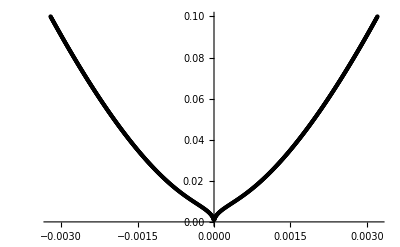
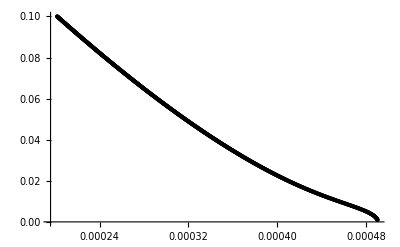

```mathematica
(* And here are the plots of ϵ in function of 'ΩSD' and 'ΓSD', but still adimensional *)

(* This is Figure 15 from Supplementary Material *)
{figΩ = ListPlot[Transpose[{ΩSDlist, ϵList}],PlotStyle->{Black}],
figΓ = ListPlot[Transpose[{ΓSDlist, ϵList}],PlotStyle->{Black}]}
```